# One patch, without effect of microbes on pollinators

This creates plots of equilibria  for the one-plant model without feedbacks between microbes and pollinators, and with low and high yeast dispersal rates (keeping bacterial dispersal rates constant). We have to redefine the plot below so I can plot equilibrium abundances by the more intuitive constant pollinator-mediated dispersal rate  instead of . This script results in the following files:

These files are used in figure 2, panels a and b, respectively.

## Load package and set working directory:

```mathematica
Needs["EcoEvo`"];
SetDirectory[NotebookDirectory[]];
SetDirectory[ParentDirectory[]<> "/_figures/_raw-nb"];
```

## Define model and set constant parameters:

```mathematica
SetModel[{Pop[Y]->{Equation:>dy PLP Y (1-Y-B)-m Y, Range:>Interval[{0,1}], Color->RGBColor["#FFCC33"]},
Pop[B]->{Equation:>(db0+db PLP) B (1-Y-B)-m B, Range:>Interval[{0,1}], Color->RGBColor["#333399"]},
Parameters:>{dy >= 0,db0 >= 0, db >= 0,m>= 0, PLP>=0}}];
db = 0.4;
db0 = 0.3;
m = 0.1;
```

## High yeast dispersal

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

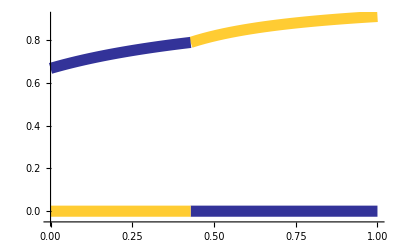

```mathematica
Clear[dy];
dy = 1.1;
p = PlotEcoEq[SolveEcoEq[],{PLP,0,1}, UnstableStyle-> {Opacity[0]}, StableStyle->{Thickness[0.02]}, 
PlotRange->{{0,1}, {-0.05, 1.5}},AxesOrigin->{0,-0.05}, 
AxesLabel->{None,None}, LabelStyle->{FontFamily->"Helvetica",16,GrayLevel[0]}]
Export[File["1patch-h0-dy1.1-equil-PLP.pdf"],p];
Clear[p];
```

## Low yeast dispersal

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

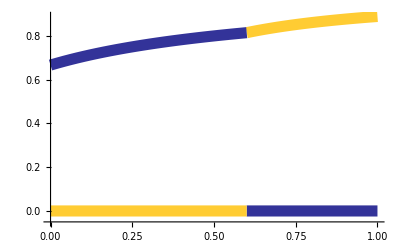

```mathematica
Clear[dy];
dy = 0.9;
p = PlotEcoEq[SolveEcoEq[],{PLP,0,1}, UnstableStyle-> {Opacity[0]}, StableStyle->{Thickness[0.02]}, PlotRange->{{0,1}, {-0.05, 1.5}},AxesOrigin->{0,-0.05}, 
AxesLabel->{None,None}, LabelStyle->{FontFamily->"Helvetica",16,GrayLevel[0]}]
Export[File["1patch-h0-dy0.9-equil-PLP.pdf"],p];
Clear[p];
```